```mathematica
Morse[x_]:=De*(1-E^(-alpha*x))^2
De=10
alpha=0.5
```

10

0.5

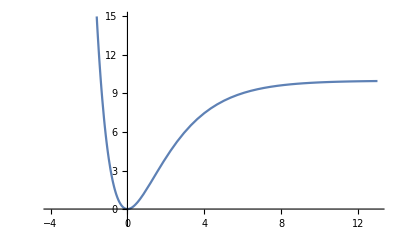

```mathematica
Plot[Morse[x],{x,-4,13},PlotRange->{-1,15}]
```

```mathematica
Morse0[x_]:=Morse[0]
```

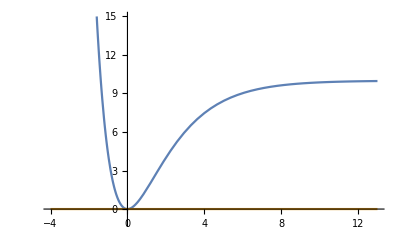

```mathematica
Plot[{Morse[x],Morse0[x]},{x,-4,13},PlotRange->{-1,15}]
```

```mathematica
D[Morse[x],x]
```

10. ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x))

```mathematica
SubMorse1[x_]:=10. ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x))
SubMorse1[0]
Morse1[x_]:=SubMorse1[0]*x+Morse0[x]
```

0.

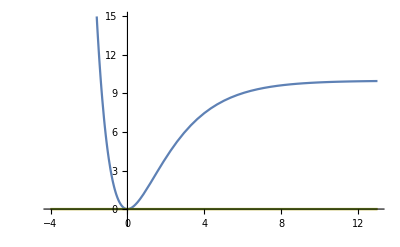

```mathematica
Plot[{Morse[x],Morse0[x],Morse1[x]},{x,-4,13},PlotRange->{-1,15}]
```

```mathematica
D[10. ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x)),x]
```

5. ⅇ^(-1. x)-5. ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x))

```mathematica
SubMorse2[x_]:=5. ⅇ^(-1. x)-5. ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x))
SubMorse2[0]
Morse2[x_]:=1/2 SubMorse2[0]*x^2+Morse1[x]
```

5.

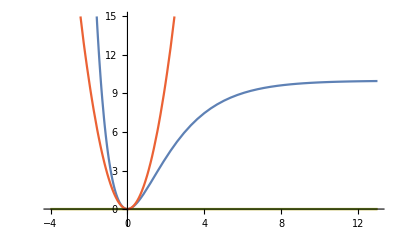

```mathematica
Plot[{Morse[x],Morse0[x],Morse1[x],Morse2[x]},{x,-4,13},PlotRange->{-1,15}]
```

```mathematica
D[5. ⅇ^(-1. x)-5. ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x)),x]
```

-7.5 ⅇ^(-1. x)+2.5 ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x))

```mathematica
SubMorse3[x_]:=-7.5 ⅇ^(-1. x)+2.5 ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x))
SubMorse3[0]
Morse3[x_]:=1/6 SubMorse3[0]*x^3+Morse2[x]
```

-7.5

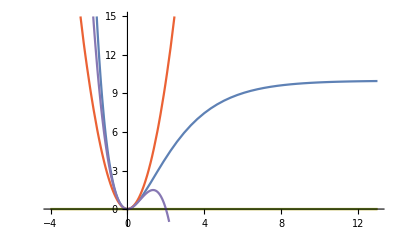

```mathematica
Plot[{Morse[x],Morse0[x],Morse1[x],Morse2[x],Morse3[x]},{x,-4,13},PlotRange->{-1,15}]
```

```mathematica
D[-7.5 ⅇ^(-1. x)+2.5 ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x)),x]
```

8.75 ⅇ^(-1. x)-1.25 ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x))

```mathematica
SubMorse4[x_]:=8.75 ⅇ^(-1. x)-1.25 ⅇ^(-0.5 x) (1-ⅇ^(-0.5 x))
SubMorse4[0]
Morse4[x_]:=1/24 SubMorse4[0]*x^4+Morse3[x]
```

8.75

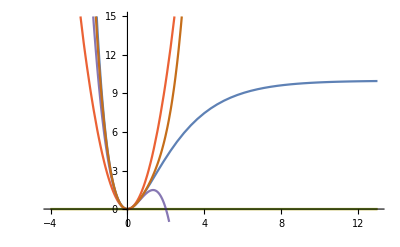

```mathematica
Plot[{Morse[x],Morse0[x],Morse1[x],Morse2[x],Morse3[x],Morse4[x]},{x,-4,13},PlotRange->{-1,15}]
```